# Finite Differencing what is h small?

The idea behind Finite Difference approximations to derivatives is simple.  Since 
	f'(x)=lim_(h->0) (f(x+h)-f(x))/h
we should be able to choose h small and use the approximation 
	f'(x)≈(f(x+h)-f(x))/h.
There are lots of other possibilities
	f'(x)≈(f(x+h)-f(x-h))/(2h)
There are wider symmetric possibilities
	f'(x)≈(-f(x+2h)+8f(x+h) - 8f(x-h)+f(x-2h))/(12h)
and 
	f'(x)≈(f(x+3h)-9f(x+2h)+ 45 f(x+h)-45 f(x-h) + 9f(x-h)+f(x-3h))/(60h)
The question is how should we choose h small

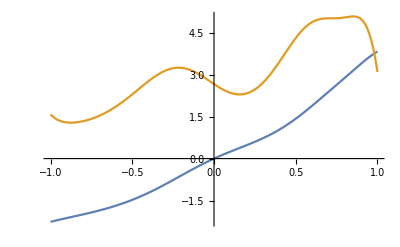

```mathematica
f[x_]:= x Cos[Sin[x^2+ 3 x+1]+ Tan[2x/2]]+2x +x^3
Plot[{f[x],f'[x]},{x,-1,1}]
```

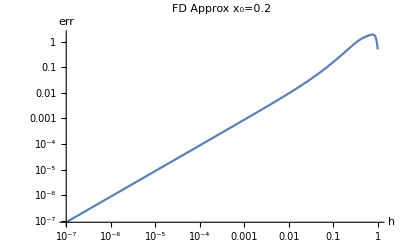

```mathematica
x0=0.2;
LogLogPlot[ {
Abs[f'[x0] - (f[x0+h]-f[x0])/h]
},
{h,10^-7,1},
PlotLabel->StringForm["FD Approx x_0=``",x0],
AxesLabel->{"h","err"}]
```